```mathematica
PacletInstall["/home/as/Fourrier/FindBounce-1.1.0.paclet"]
```

PacletInstall::samevers: A paclet named FindBounce with the same version number (1.1.0) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with ForceVersionInstall -> True.

$Failed

```mathematica
Needs["FindBounce`"]
```

```mathematica
PacletFind["FindBounce"]
```

{PacletObject[…]}

```mathematica
Names["FindBounce`*"]
```

{BounceFunction,BouncePlot,FindBounce}

```mathematica
?FindBounce
?BounceFunction
?BouncePlot
```

### Test Run

```mathematica
lambda=0.3;
epsilon=0.1;

V[h_,s_]:=((h^2-1)^2)/4+((s^2-1)^2)/4+lambda h^2 s^2-epsilon h;

vars={h,s};

phiTrue={0.89427236,0.72122546};
phiFalse={-0.60590553,0.88302157};

dummyPath=Table[{(1-t)*phiFalse[[1]]+t*phiTrue[[1]]+0.25*Sin[Pi*t],(1-t)*phiFalse[[2]]+t*phiTrue[[2]]-0.15*Sin[Pi*t]},{t,0,1,1/30}];

bf=FindBounce[V[h,s],vars,{phiFalse,phiTrue},"FieldPoints"->dummyPath];

bf["Action"]
```

274.487

### Initial Path Modified

```mathematica
Directory[]
```

/home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier

```mathematica
SetDirectory@NotebookDirectory[]
```

/home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier

```mathematica
Get["findbounce_csvK_scan_READY.wl"];
```

Current directory = /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier

Output file will be = /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_results.csv

Methods = {straight,csvK1,csvK2,csvK3,csvK4,csvK5,csvK6,csvK7,csvK8}

N list = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

Time limit per FindBounce call = 120 seconds

============================================

Running FindBounce nphi = 1

Vfalse = 0.

Vtrue  = -0.335501

DeltaV = 0.335501

method = straight

status = failed   action = —   time = 0.0196 s

method = csvK1

status = failed   action = —   time = 0.0200 s

method = csvK2

status = failed   action = —   time = 0.0193 s

method = csvK3

status = failed   action = —   time = 0.0193 s

method = csvK4

status = failed   action = —   time = 0.0195 s

method = csvK5

status = failed   action = —   time = 0.0193 s

method = csvK6

status = failed   action = —   time = 0.0195 s

method = csvK7

status = failed   action = —   time = 0.0193 s

method = csvK8

status = failed   action = —   time = 0.0193 s

============================================

Running FindBounce nphi = 2

Vfalse = 0.

Vtrue  = -1.37135

DeltaV = 1.37135

method = straight

status = ok   action = 17.3478   time = 0.2799 s

method = csvK1

status = failed   action = —   time = 0.0039 s

method = csvK2

status = failed   action = —   time = 0.0034 s

method = csvK3

status = failed   action = —   time = 0.0033 s

method = csvK4

status = failed   action = —   time = 0.0033 s

method = csvK5

status = failed   action = —   time = 0.0033 s

method = csvK6

status = failed   action = —   time = 0.0033 s

method = csvK7

status = failed   action = —   time = 0.0034 s

method = csvK8

status = ok   action = 0.388109   time = 0.1641 s

============================================

Running FindBounce nphi = 3

Vfalse = 0.

Vtrue  = -2.46805

DeltaV = 2.46805

method = straight

status = ok   action = 38.7261   time = 0.1191 s

method = csvK1

status = failed   action = —   time = 0.0041 s

method = csvK2

status = failed   action = —   time = 0.0036 s

method = csvK3

status = failed   action = —   time = 0.0035 s

method = csvK4

status = failed   action = —   time = 0.1028 s

method = csvK5

status = ok   action = 18.0508   time = 0.0910 s

method = csvK6

status = ok   action = 20.3216   time = 0.0985 s

method = csvK7

status = ok   action = 20.802   time = 0.1082 s

method = csvK8

status = ok   action = 26.9842   time = 0.1086 s

============================================

Running FindBounce nphi = 4

Vfalse = 0.

Vtrue  = -0.835294

DeltaV = 0.835294

method = straight

status = ok   action = 1284.47   time = 0.0726 s

method = csvK1

status = ok   action = 1075.71   time = 0.0244 s

method = csvK2

status = ok   action = 1176.86   time = 0.0353 s

method = csvK3

status = ok   action = 1210.06   time = 0.0481 s

method = csvK4

status = ok   action = 1225.85   time = 0.0585 s

method = csvK5

status = ok   action = 1245.61   time = 0.0692 s

method = csvK6

status = ok   action = 1300.06   time = 0.0748 s

method = csvK7

status = ok   action = 1308.61   time = 0.0257 s

method = csvK8

status = ok   action = 1298.89   time = 0.0279 s

============================================

Running FindBounce nphi = 5

Vfalse = 0.

Vtrue  = -3.46971

DeltaV = 3.46971

method = straight

status = ok   action = 164.247   time = 0.1323 s

method = csvK1

status = failed   action = —   time = 0.0036 s

method = csvK2

status = ok   action = 0.21887   time = 0.0976 s

method = csvK3

status = ok   action = 87.8885   time = 0.0695 s

method = csvK4

status = ok   action = 35.2907   time = 0.1042 s

method = csvK5

status = ok   action = 55.7611   time = 0.1161 s

method = csvK6

status = ok   action = 112.974   time = 0.1238 s

method = csvK7

status = ok   action = 154.084   time = 0.1288 s

method = csvK8

status = ok   action = 165.575   time = 0.1302 s

============================================

Running FindBounce nphi = 6

Vfalse = 0.

Vtrue  = -3.7323

DeltaV = 3.7323

method = straight

status = ok   action = 310.56   time = 0.1262 s

method = csvK1

status = failed   action = —   time = 0.0037 s

method = csvK2

status = ok   action = 223.702   time = 0.0445 s

method = csvK3

status = ok   action = 278.796   time = 0.0618 s

method = csvK4

status = ok   action = 279.696   time = 0.0770 s

method = csvK5

status = ok   action = 278.476   time = 0.1023 s

method = csvK6

status = ok   action = 294.427   time = 0.1137 s

method = csvK7

status = ok   action = 302.295   time = 0.1240 s

method = csvK8

status = ok   action = 315.026   time = 0.0728 s

============================================

Running FindBounce nphi = 7

Vfalse = 0.

Vtrue  = -0.80376

DeltaV = 0.80376

method = straight

status = ok   action = 24616.4   time = 0.1130 s

method = csvK1

status = ok   action = 24227.8   time = 0.0128 s

method = csvK2

status = ok   action = 24387.6   time = 0.0546 s

method = csvK3

status = ok   action = 23521.3   time = 0.0785 s

method = csvK4

status = ok   action = 24144.4   time = 0.0894 s

method = csvK5

status = ok   action = 24923.9   time = 0.0997 s

method = csvK6

status = ok   action = 25375.2   time = 0.1119 s

method = csvK7

status = ok   action = 25349.7   time = 0.0698 s

method = csvK8

status = ok   action = 24993.7   time = 0.0522 s

============================================

Running FindBounce nphi = 8

Vfalse = 0.

Vtrue  = -3.73111

DeltaV = 3.73111

method = straight

status = ok   action = 1091.88   time = 0.1379 s

method = csvK1

status = ok   action = 832.452   time = 0.0497 s

method = csvK2

status = ok   action = 982.563   time = 0.0506 s

method = csvK3

status = ok   action = 1028.34   time = 0.0841 s

method = csvK4

status = ok   action = 1040.86   time = 0.1077 s

method = csvK5

status = ok   action = 1120.32   time = 0.0390 s

method = csvK6

status = ok   action = 1113.43   time = 0.0421 s

method = csvK7

status = ok   action = 1111.91   time = 0.0449 s

method = csvK8

status = ok   action = 1103.73   time = 0.0485 s

============================================

Running FindBounce nphi = 9

Vfalse = 0.

Vtrue  = -3.66509

DeltaV = 3.66509

method = straight

status = ok   action = 1919.89   time = 0.1586 s

method = csvK1

status = ok   action = 1667.21   time = 0.0577 s

method = csvK2

status = ok   action = 1817.54   time = 0.0666 s

method = csvK3

status = ok   action = 1825.2   time = 0.0924 s

method = csvK4

status = ok   action = 1861.7   time = 0.1207 s

method = csvK5

status = ok   action = 1976.58   time = 0.0669 s

method = csvK6

status = ok   action = 1958.81   time = 0.0449 s

method = csvK7

status = ok   action = 1957.24   time = 0.0485 s

method = csvK8

status = ok   action = 1942.73   time = 0.0546 s

============================================

Running FindBounce nphi = 10

Vfalse = 0.

Vtrue  = -5.60393

DeltaV = 5.60393

method = straight

status = ok   action = 1156.5   time = 0.1894 s

method = csvK1

status = ok   action = 865.354   time = 0.0796 s

method = csvK2

status = ok   action = 1043.01   time = 0.0775 s

method = csvK3

status = ok   action = 1123.56   time = 0.1001 s

method = csvK4

status = ok   action = 1121.94   time = 0.1301 s

method = csvK5

status = ok   action = 1186.61   time = 0.0486 s

method = csvK6

status = ok   action = 1179.5   time = 0.0537 s

method = csvK7

status = ok   action = 1177.93   time = 0.0576 s

method = csvK8

status = ok   action = 1169.25   time = 0.0622 s

============================================

Running FindBounce nphi = 11

Vfalse = 0.

Vtrue  = -7.30705

DeltaV = 7.30705

method = straight

status = ok   action = 937.693   time = 0.2219 s

method = csvK1

status = failed   action = —   time = 0.0652 s

method = csvK2

status = ok   action = 827.441   time = 0.0779 s

method = csvK3

status = ok   action = 903.492   time = 0.1168 s

method = csvK4

status = ok   action = 905.789   time = 0.1632 s

method = csvK5

status = ok   action = 962.275   time = 0.0650 s

method = csvK6

status = ok   action = 955.587   time = 0.0671 s

method = csvK7

status = ok   action = 954.041   time = 0.0645 s

method = csvK8

status = ok   action = 947.186   time = 0.0730 s

============================================

Running FindBounce nphi = 12

Vfalse = 0.

Vtrue  = -4.81274

DeltaV = 4.81274

method = straight

status = ok   action = 3300.97   time = 0.2941 s

method = csvK1

status = ok   action = 3092.96   time = 0.0941 s

method = csvK2

status = ok   action = 3286.76   time = 0.0879 s

method = csvK3

status = ok   action = 3308.86   time = 0.1436 s

method = csvK4

status = ok   action = 3371.79   time = 0.1874 s

method = csvK5

status = ok   action = 3395.59   time = 0.0590 s

method = csvK6

status = ok   action = 3367.72   time = 0.0672 s

method = csvK7

status = ok   action = 3366.74   time = 0.0838 s

method = csvK8

status = ok   action = 3340.75   time = 0.1264 s

============================================

Running FindBounce nphi = 13

Vfalse = 0.

Vtrue  = -7.07821

DeltaV = 7.07821

method = straight

status = ok   action = 1982.94   time = 0.5273 s

method = csvK1

status = ok   action = 1664.02   time = 0.1326 s

method = csvK2

status = ok   action = 1923.09   time = 0.1174 s

method = csvK3

status = ok   action = 2034.37   time = 0.1916 s

method = csvK4

status = ok   action = 2035.56   time = 0.2200 s

method = csvK5

status = ok   action = 2042.2   time = 0.0777 s

method = csvK6

status = ok   action = 2028.99   time = 0.1207 s

method = csvK7

status = ok   action = 2025.59   time = 0.1277 s

method = csvK8

status = ok   action = 2004.93   time = 0.1374 s

============================================

Running FindBounce nphi = 14

Vfalse = 0.

Vtrue  = -7.52703

DeltaV = 7.52703

method = straight

status = ok   action = 2503.84   time = 0.6216 s

method = csvK1

status = ok   action = 2234.21   time = 0.1417 s

method = csvK2

status = ok   action = 2463.17   time = 0.1285 s

method = csvK3

status = ok   action = 2586.04   time = 0.1824 s

method = csvK4

status = ok   action = 2576.02   time = 0.2562 s

method = csvK5

status = ok   action = 2578.74   time = 0.0849 s

method = csvK6

status = ok   action = 2555.67   time = 0.0956 s

method = csvK7

status = ok   action = 2553.77   time = 0.1146 s

method = csvK8

status = ok   action = 2534.1   time = 0.1633 s

============================================

Running FindBounce nphi = 15

Vfalse = 0.

Vtrue  = -4.61349

DeltaV = 4.61349

method = straight

status = ok   action = 11721.9   time = 0.5167 s

method = csvK1

status = ok   action = 11782.   time = 0.0685 s

method = csvK2

status = ok   action = 12058.8   time = 0.1464 s

method = csvK3

status = ok   action = 11682.7   time = 0.2321 s

method = csvK4

status = ok   action = 12167.6   time = 0.3478 s

method = csvK5

status = ok   action = 12117.6   time = 0.1787 s

method = csvK6

status = ok   action = 11947.   time = 0.1072 s

method = csvK7

status = ok   action = 11958.2   time = 0.1209 s

method = csvK8

status = ok   action = 11856.9   time = 0.1311 s

============================================

Running FindBounce nphi = 16

Vfalse = 0.

Vtrue  = -9.00462

DeltaV = 9.00462

method = straight

status = ok   action = 3038.92   time = 0.5312 s

method = csvK1

status = ok   action = 2827.01   time = 0.2014 s

method = csvK2

status = ok   action = 3006.49   time = 0.1745 s

method = csvK3

status = ok   action = 3147.81   time = 0.2359 s

method = csvK4

status = ok   action = 3121.93   time = 0.3387 s

method = csvK5

status = ok   action = 3125.73   time = 0.1135 s

method = csvK6

status = ok   action = 3101.17   time = 0.1276 s

method = csvK7

status = ok   action = 3099.96   time = 0.1403 s

method = csvK8

status = ok   action = 3071.38   time = 0.1594 s

============================================

Running FindBounce nphi = 17

Vfalse = 0.

Vtrue  = -8.61869

DeltaV = 8.61869

method = straight

status = ok   action = 4583.29   time = 0.5913 s

method = csvK1

status = ok   action = 4475.22   time = 0.2163 s

method = csvK2

status = ok   action = 4603.24   time = 0.1784 s

method = csvK3

status = ok   action = 4585.39   time = 0.2936 s

method = csvK4

status = ok   action = 4710.8   time = 0.3503 s

method = csvK5

status = ok   action = 4705.53   time = 0.1213 s

method = csvK6

status = ok   action = 4674.08   time = 0.1353 s

method = csvK7

status = ok   action = 4675.11   time = 0.1518 s

method = csvK8

status = ok   action = 4633.43   time = 0.1656 s

============================================

Running FindBounce nphi = 18

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 19

Vfalse = 0.

Vtrue  = -3.82474

DeltaV = 3.82474

method = straight

status = ok   action = 60078.4   time = 0.6568 s

method = csvK1

status = ok   action = 60295.   time = 0.0620 s

method = csvK2

status = ok   action = 62888.5   time = 0.2250 s

method = csvK3

status = ok   action = 60203.7   time = 0.3743 s

method = csvK4

status = ok   action = 63225.9   time = 0.4945 s

method = csvK5

status = ok   action = 62908.5   time = 0.6248 s

method = csvK6

status = ok   action = 61793.9   time = 0.2384 s

method = csvK7

status = ok   action = 61098.4   time = 0.1963 s

method = csvK8

status = ok   action = 60662.4   time = 0.2236 s

============================================

Running FindBounce nphi = 20

Vfalse = 0.

Vtrue  = -9.18465

DeltaV = 9.18465

method = straight

status = ok   action = 8285.   time = 0.8302 s

method = csvK1

status = ok   action = 8197.76   time = 0.1306 s

method = csvK2

status = ok   action = 8473.65   time = 0.2613 s

method = csvK3

status = ok   action = 8295.45   time = 0.4273 s

method = csvK4

status = ok   action = 8550.46   time = 0.4945 s

method = csvK5

status = ok   action = 8611.22   time = 0.2374 s

method = csvK6

status = ok   action = 8431.64   time = 0.1914 s

method = csvK7

status = ok   action = 8439.94   time = 0.2141 s

method = csvK8

status = ok   action = 8369.41   time = 0.2404 s

============================================

Running FindBounce nphi = 21

Vfalse = 0.

Vtrue  = -11.122

DeltaV = 11.122

method = straight

status = ok   action = 6279.52   time = 0.9177 s

method = csvK1

status = ok   action = 6185.35   time = 0.2694 s

method = csvK2

status = ok   action = 6392.69   time = 0.2844 s

method = csvK3

status = ok   action = 6321.25   time = 0.4735 s

method = csvK4

status = ok   action = 6531.82   time = 0.5610 s

method = csvK5

status = ok   action = 6506.   time = 0.2776 s

method = csvK6

status = ok   action = 6380.11   time = 0.2187 s

method = csvK7

status = ok   action = 6386.78   time = 0.2442 s

method = csvK8

status = ok   action = 6335.22   time = 0.2684 s

============================================

Running FindBounce nphi = 22

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 23

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 24

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 25

Vfalse = 0.

Vtrue  = -14.3324

DeltaV = 14.3324

method = straight

status = ok   action = 7504.83   time = 1.3806 s

method = csvK1

status = ok   action = 7401.03   time = 0.3082 s

method = csvK2

status = ok   action = 7663.65   time = 0.4262 s

method = csvK3

status = ok   action = 7548.16   time = 0.7308 s

method = csvK4

status = ok   action = 7970.97   time = 0.7634 s

method = csvK5

status = ok   action = 7779.76   time = 0.4087 s

method = csvK6

status = ok   action = 7619.03   time = 0.3294 s

method = csvK7

status = ok   action = 7628.99   time = 0.3692 s

method = csvK8

status = ok   action = 7569.65   time = 0.4079 s

============================================

Running FindBounce nphi = 26

Vfalse = 0.

Vtrue  = -13.4668

DeltaV = 13.4668

method = straight

status = ok   action = 10361.7   time = 1.5203 s

method = csvK1

status = ok   action = 10249.   time = 0.2273 s

method = csvK2

status = ok   action = 10634.   time = 0.4576 s

method = csvK3

status = ok   action = 10384.3   time = 0.8126 s

method = csvK4

status = ok   action = 10745.9   time = 0.9759 s

method = csvK5

status = ok   action = 10761.6   time = 0.4557 s

method = csvK6

status = ok   action = 10513.3   time = 0.3670 s

method = csvK7

status = ok   action = 10529.5   time = 0.4152 s

method = csvK8

status = ok   action = 10451.4   time = 0.4595 s

============================================

Running FindBounce nphi = 27

Vfalse = 0.

Vtrue  = -11.62

DeltaV = 11.62

method = straight

status = ok   action = 18795.9   time = 1.6647 s

method = csvK1

status = ok   action = 18680.2   time = 0.1297 s

method = csvK2

status = ok   action = 19495.8   time = 0.4940 s

method = csvK3

status = ok   action = 18815.4   time = 0.9067 s

method = csvK4

status = ok   action = 19476.4   time = 1.0738 s

method = csvK5

status = ok   action = 19586.7   time = 0.5036 s

method = csvK6

status = ok   action = 19267.8   time = 0.5784 s

method = csvK7

status = ok   action = 19094.9   time = 0.4586 s

method = csvK8

status = ok   action = 18958.1   time = 0.5015 s

============================================

Running FindBounce nphi = 28

Vfalse = 0.

Vtrue  = -16.4698

DeltaV = 16.4698

method = straight

status = ok   action = 9395.58   time = 1.8239 s

method = csvK1

status = ok   action = 9281.77   time = 0.2782 s

method = csvK2

status = ok   action = 9626.72   time = 0.5529 s

method = csvK3

status = ok   action = 9418.67   time = 0.9899 s

method = csvK4

status = ok   action = 10001.2   time = 1.0419 s

method = csvK5

status = ok   action = 9755.54   time = 0.5620 s

method = csvK6

status = ok   action = 9537.79   time = 0.4479 s

method = csvK7

status = ok   action = 9551.32   time = 0.4999 s

method = csvK8

status = ok   action = 9478.87   time = 0.5435 s

============================================

Running FindBounce nphi = 29

Vfalse = 0.

Vtrue  = -14.4175

DeltaV = 14.4175

method = straight

status = ok   action = 15048.6   time = 1.9963 s

method = csvK1

status = ok   action = 15162.4   time = 0.2255 s

method = csvK2

status = ok   action = 15582.3   time = 0.5947 s

method = csvK3

status = ok   action = 15167.2   time = 1.0850 s

method = csvK4

status = ok   action = 16133.1   time = 1.1334 s

method = csvK5

status = ok   action = 15655.   time = 0.6047 s

method = csvK6

status = ok   action = 15404.1   time = 0.6999 s

method = csvK7

status = ok   action = 15277.2   time = 0.5397 s

method = csvK8

status = ok   action = 15168.9   time = 0.5902 s

============================================

Running FindBounce nphi = 30

Vfalse = 0.

Vtrue  = -12.4285

DeltaV = 12.4285

method = straight

status = ok   action = 26249.6   time = 2.1676 s

method = csvK1

status = ok   action = 26051.8   time = 0.1684 s

method = csvK2

status = ok   action = 27340.1   time = 0.6538 s

method = csvK3

status = ok   action = 26221.5   time = 1.1923 s

method = csvK4

status = ok   action = 27143.9   time = 1.4251 s

method = csvK5

status = ok   action = 26854.   time = 0.8696 s

method = csvK6

status = ok   action = 26914.3   time = 0.7484 s

method = csvK7

status = ok   action = 26815.4   time = 0.8261 s

method = csvK8

status = ok   action = 26434.2   time = 0.6410 s

============================================

Running FindBounce nphi = 31

Vfalse = 0.

Vtrue  = -12.3008

DeltaV = 12.3008

method = straight

status = ok   action = 32462.5   time = 2.3643 s

method = csvK1

status = ok   action = 32333.4   time = 0.1878 s

method = csvK2

status = ok   action = 33880.7   time = 0.7175 s

method = csvK3

status = ok   action = 32423.3   time = 1.3051 s

method = csvK4

status = ok   action = 33562.4   time = 1.5612 s

method = csvK5

status = ok   action = 33214.9   time = 0.9356 s

method = csvK6

status = ok   action = 33312.4   time = 0.8085 s

method = csvK7

status = ok   action = 33192.2   time = 0.8957 s

method = csvK8

status = ok   action = 32701.8   time = 0.6979 s

============================================

Running FindBounce nphi = 32

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 33

Vfalse = 0.

Vtrue  = -9.56226

DeltaV = 9.56226

method = straight

status = ok   action = 88416.5   time = 2.5111 s

method = csvK1

status = ok   action = 88708.   time = 0.2220 s

method = csvK2

status = ok   action = 96516.7   time = 0.7229 s

method = csvK3

status = ok   action = 87995.4   time = 1.5470 s

method = csvK4

status = ok   action = 95557.3   time = 1.6178 s

method = csvK5

status = ok   action = 92585.6   time = 0.8395 s

method = csvK6

status = ok   action = 90942.7   time = 0.9409 s

method = csvK7

status = ok   action = 89704.7   time = 0.7374 s

method = csvK8

status = ok   action = 89140.   time = 0.8122 s

============================================

Running FindBounce nphi = 34

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 35

Vfalse = 0.

Vtrue  = -5.3158

DeltaV = 5.3158

method = straight

status = ok   action = 660121.   time = 2.9268 s

method = csvK1

status = ok   action = 666139.   time = 0.2619 s

method = csvK2

status = ok   action = 719885.   time = 0.8503 s

method = csvK3

status = ok   action = 727771.   time = 1.5813 s

method = csvK4

status = ok   action = 713244.   time = 1.8446 s

method = csvK5

status = ok   action = 673263.   time = 0.6823 s

method = csvK6

status = ok   action = 670467.   time = 0.7689 s

method = csvK7

status = ok   action = 670758.   time = 0.8523 s

method = csvK8

status = ok   action = 666664.   time = 0.9380 s

============================================

Running FindBounce nphi = 36

Vfalse = 0.

Vtrue  = -15.3579

DeltaV = 15.3579

method = straight

status = ok   action = 42031.4   time = 3.1501 s

method = csvK1

status = ok   action = 42011.2   time = 0.2714 s

method = csvK2

status = ok   action = 45868.5   time = 0.9084 s

method = csvK3

status = ok   action = 42004.5   time = 1.9251 s

method = csvK4

status = ok   action = 45328.6   time = 1.9787 s

method = csvK5

status = ok   action = 43946.6   time = 1.0355 s

method = csvK6

status = ok   action = 42591.5   time = 0.8267 s

method = csvK7

status = ok   action = 42658.7   time = 0.9158 s

method = csvK8

status = ok   action = 42377.4   time = 1.0099 s

============================================

Running FindBounce nphi = 37

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 38

Vfalse = 0.

Vtrue  = -20.9064

DeltaV = 20.9064

method = straight

status = ok   action = 25444.8   time = 3.9781 s

method = csvK1

status = ok   action = 25320.7   time = 0.3273 s

method = csvK2

status = ok   action = 27728.9   time = 1.1124 s

method = csvK3

status = ok   action = 25431.9   time = 2.2154 s

method = csvK4

status = ok   action = 27352.4   time = 2.2810 s

method = csvK5

status = ok   action = 26563.8   time = 1.2091 s

method = csvK6

status = ok   action = 25793.7   time = 0.9549 s

method = csvK7

status = ok   action = 25836.5   time = 1.0708 s

method = csvK8

status = ok   action = 25659.   time = 1.1536 s

============================================

Running FindBounce nphi = 39

Vfalse = 0.

Vtrue  = -15.7992

DeltaV = 15.7992

method = straight

status = ok   action = 62410.3   time = 3.9948 s

method = csvK1

status = ok   action = 62620.5   time = 0.3456 s

method = csvK2

status = ok   action = 68132.8   time = 1.1825 s

method = csvK3

status = ok   action = 68663.2   time = 2.0537 s

method = csvK4

status = ok   action = 67304.8   time = 2.4397 s

method = csvK5

status = ok   action = 65311.3   time = 1.2644 s

method = csvK6

status = ok   action = 63296.6   time = 1.0490 s

method = csvK7

status = ok   action = 63381.5   time = 1.1423 s

method = csvK8

status = ok   action = 62955.3   time = 1.2505 s

============================================

Running FindBounce nphi = 40

Vfalse = 0.

Vtrue  = -15.5703

DeltaV = 15.5703

method = straight

status = ok   action = 76145.6   time = 4.1906 s

method = csvK1

status = ok   action = 76507.1   time = 0.3701 s

method = csvK2

status = ok   action = 83165.8   time = 1.2325 s

method = csvK3

status = ok   action = 84223.8   time = 2.1408 s

method = csvK4

status = ok   action = 82155.9   time = 2.5343 s

method = csvK5

status = ok   action = 77550.5   time = 0.9332 s

method = csvK6

status = ok   action = 77242.9   time = 1.0585 s

method = csvK7

status = ok   action = 77340.9   time = 1.1855 s

method = csvK8

status = ok   action = 76819.2   time = 1.2983 s

============================================

Running FindBounce nphi = 41

Vfalse = 0.

Vtrue  = -9.57927

DeltaV = 9.57927

method = straight

status = ok   action = 343148.   time = 4.4437 s

method = csvK1

status = ok   action = 345942.   time = 0.3892 s

method = csvK2

status = ok   action = 390786.   time = 1.0203 s

method = csvK3

status = ok   action = 378102.   time = 2.2716 s

method = csvK4

status = ok   action = 370414.   time = 1.9973 s

method = csvK5

status = ok   action = 350169.   time = 1.0267 s

method = csvK6

status = ok   action = 348660.   time = 1.1346 s

method = csvK7

status = ok   action = 348862.   time = 1.3217 s

method = csvK8

status = ok   action = 346613.   time = 1.3963 s

============================================

Running FindBounce nphi = 42

Vfalse = 0.

Vtrue  = -7.08601

DeltaV = 7.08601

method = straight

status = ok   action = 889768.   time = 4.7824 s

method = csvK1

status = ok   action = 901989.   time = 0.4285 s

method = csvK2

status = ok   action = 1.01782×10^6   time = 1.1115 s

method = csvK3

status = ok   action = 983050.   time = 2.4605 s

method = csvK4

status = ok   action = 907661.   time = 0.9038 s

method = csvK5

status = ok   action = 908462.   time = 1.0630 s

method = csvK6

status = ok   action = 904364.   time = 1.1994 s

method = csvK7

status = ok   action = 904935.   time = 1.3478 s

method = csvK8

status = ok   action = 899024.   time = 1.5485 s

============================================

Running FindBounce nphi = 43

Vfalse = 0.

Vtrue  = -25.0458

DeltaV = 25.0458

method = straight

status = ok   action = 30846.6   time = 5.2679 s

method = csvK1

status = ok   action = 30829.2   time = 0.4600 s

method = csvK2

status = ok   action = 33790.7   time = 1.4561 s

method = csvK3

status = ok   action = 31035.4   time = 2.9138 s

method = csvK4

status = ok   action = 33250.   time = 2.2090 s

method = csvK5

status = ok   action = 32211.8   time = 1.6674 s

method = csvK6

status = ok   action = 31254.4   time = 1.2726 s

method = csvK7

status = ok   action = 31311.4   time = 1.4384 s

method = csvK8

status = ok   action = 31093.5   time = 1.5735 s

============================================

Running FindBounce nphi = 44

Vfalse = 0.

Vtrue  = -23.8642

DeltaV = 23.8642

method = straight

status = ok   action = 39052.8   time = 5.9582 s

method = csvK1

status = ok   action = 39084.6   time = 0.4737 s

method = csvK2

status = ok   action = 42750.7   time = 1.5036 s

method = csvK3

status = ok   action = 43200.4   time = 2.8005 s

method = csvK4

status = ok   action = 42140.4   time = 2.4188 s

method = csvK5

status = ok   action = 40811.7   time = 1.7693 s

method = csvK6

status = ok   action = 39570.6   time = 1.4084 s

method = csvK7

status = ok   action = 39638.6   time = 1.5303 s

method = csvK8

status = ok   action = 39369.3   time = 1.7091 s

============================================

Running FindBounce nphi = 45

Vfalse = 0.

Vtrue  = -8.38423

DeltaV = 8.38423

method = straight

status = ok   action = 770569.   time = 5.8716 s

method = csvK1

status = ok   action = 780975.   time = 0.5132 s

method = csvK2

status = ok   action = 882557.   time = 1.2658 s

method = csvK3

status = ok   action = 856537.   time = 2.9145 s

method = csvK4

status = ok   action = 827398.   time = 1.6278 s

method = csvK5

status = ok   action = 785464.   time = 1.3178 s

method = csvK6

status = ok   action = 782264.   time = 1.4588 s

method = csvK7

status = ok   action = 782860.   time = 1.6912 s

method = csvK8

status = ok   action = 778138.   time = 1.8468 s

============================================

Running FindBounce nphi = 46

Vfalse = 0.

Vtrue  = -10.654

DeltaV = 10.654

method = straight

status = ok   action = 451834.   time = 6.1781 s

method = csvK1

status = ok   action = 457228.   time = 0.5414 s

method = csvK2

status = ok   action = 517536.   time = 1.3515 s

method = csvK3

status = ok   action = 503712.   time = 3.0526 s

method = csvK4

status = ok   action = 489815.   time = 2.6985 s

method = csvK5

status = ok   action = 460223.   time = 1.3943 s

method = csvK6

status = ok   action = 458409.   time = 1.5616 s

method = csvK7

status = ok   action = 458815.   time = 1.7528 s

method = csvK8

status = ok   action = 456092.   time = 1.9539 s

============================================

Running FindBounce nphi = 47

Vfalse = 0.

Vtrue  = -4.20425

DeltaV = 4.20425

method = straight

status = ok   action = 7.24066×10^6   time = 7.1614 s

method = csvK1

status = ok   action = 7.37429×10^6   time = 0.5656 s

method = csvK2

status = ok   action = 8.31151×10^6   time = 1.4466 s

method = csvK3

status = ok   action = 8.03568×10^6   time = 3.2569 s

method = csvK4

status = ok   action = 7.38797×10^6   time = 1.2423 s

method = csvK5

status = ok   action = 7.39216×10^6   time = 1.4503 s

method = csvK6

status = ok   action = 7.35991×10^6   time = 1.6699 s

method = csvK7

status = ok   action = 7.36433×10^6   time = 1.8286 s

method = csvK8

status = ok   action = 7.31848×10^6   time = 2.0926 s

============================================

Running FindBounce nphi = 48

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 49

Vfalse = 0.

Vtrue  = -29.0471

DeltaV = 29.0471

method = straight

status = ok   action = 39610.5   time = 7.9330 s

method = csvK1

status = ok   action = 39643.2   time = 0.6320 s

method = csvK2

status = ok   action = 43677.2   time = 2.0091 s

method = csvK3

status = ok   action = 39915.9   time = 4.1472 s

method = csvK4

status = ok   action = 42852.1   time = 3.2001 s

method = csvK5

status = ok   action = 41361.8   time = 2.3608 s

method = csvK6

status = ok   action = 40023.1   time = 1.8781 s

method = csvK7

status = ok   action = 40115.4   time = 2.1053 s

method = csvK8

status = ok   action = 39861.8   time = 2.2638 s

============================================

Running FindBounce nphi = 50

Vfalse = 0.

Vtrue  = -29.5609

DeltaV = 29.5609

method = straight

status = ok   action = 41878.4   time = 8.4210 s

method = csvK1

status = ok   action = 41922.2   time = 0.6645 s

method = csvK2

status = ok   action = 46121.2   time = 2.1341 s

method = csvK3

status = ok   action = 42171.8   time = 4.4288 s

method = csvK4

status = ok   action = 45309.5   time = 3.3467 s

method = csvK5

status = ok   action = 43744.2   time = 2.5062 s

method = csvK6

status = ok   action = 42330.6   time = 1.9974 s

method = csvK7

status = ok   action = 42423.7   time = 2.2435 s

method = csvK8

status = ok   action = 42154.8   time = 2.4081 s

Saved results to: /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_results.csv

================ SUMMARY TABLE ================

Saved raw results to: /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_results.csv

Saved summary to: /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_summary.csv

DONE. To see CSV files here, run: FileNames["*.csv", Directory[]]

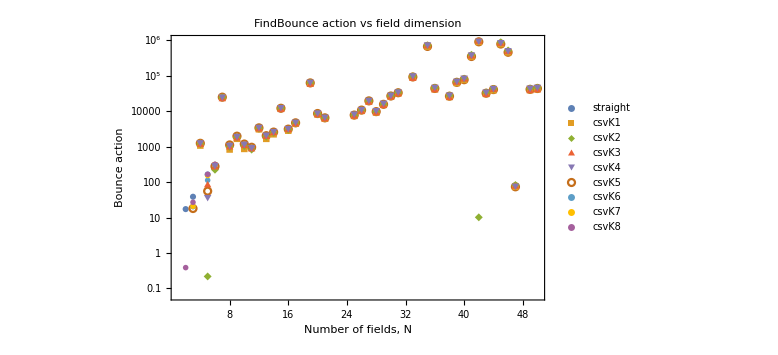

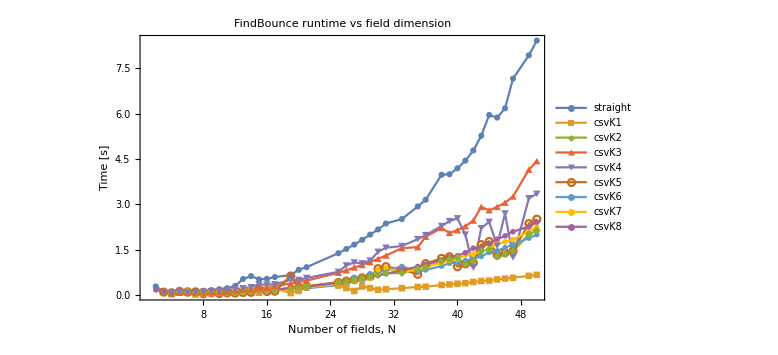

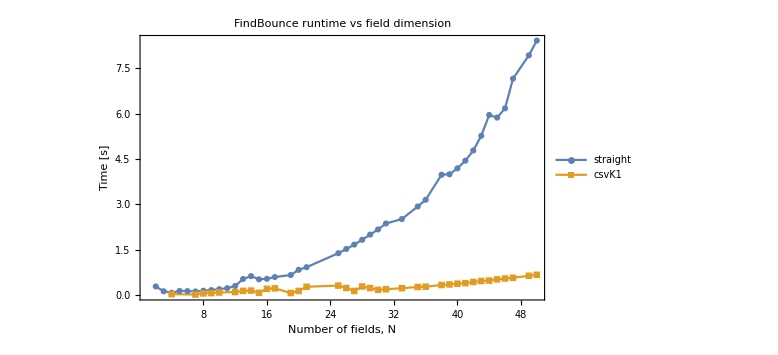

```mathematica
file="findbounce_csvK_scan_results.csv";
raw=Import[file,"CSV"];

head=raw[[1]];
rows=AssociationThread[head->#]&/@raw[[2;;]];

clean[x_]:=StringReplace[ToString[x],"\""->""];
num[x_]:=Quiet@Check[ToExpression[clean[x]],Missing["NA"]];

data=Association[#,"n"->num[#["nphi"]],"method2"->clean[#["method"]],"status2"->clean[#["status"]],"action"->num[#["ActionFindBounceD4"]],"time"->num[#["TimeSeconds"]]]&/@rows;

good=Select[data,#["status2"]=="ok"&&NumberQ[#["n"]]&&NumberQ[#["time"]]&];

methods={"straight","csvK1","csvK2","csvK3","csvK4","csvK5","csvK6","csvK7","csvK8"};

series[col_,m_]:=SortBy[({#["n"],#[col]}&/@Select[good,#["method2"]==m&&NumberQ[#[col]]&]),First];

pAction=ListLogPlot[series["action",#]&/@methods,PlotLegends->Placed[methods,Right],Frame->True,FrameLabel->{"Number of fields, N","Bounce action"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large,PlotLabel->"FindBounce action vs field dimension"];

pTime=ListLinePlot[series["time",#]&/@methods,PlotLegends->Placed[methods,Right],Frame->True,FrameLabel->{"Number of fields, N","Time [s]"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large,PlotLabel->"FindBounce runtime vs field dimension"];

methods2 = {"straight","csvK1"};
pTime2=ListLinePlot[series["time",#]&/@methods2,PlotLegends->Placed[methods,Right],Frame->True,FrameLabel->{"Number of fields, N","Time [s]"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large,PlotLabel->"FindBounce runtime vs field dimension"];

pAction
pTime
pTime2

plotDir=FileNameJoin[{NotebookDirectory[],"Plots"}];
If[!DirectoryQ[plotDir],CreateDirectory[plotDir]];

Export[FileNameJoin[{plotDir,"findbounce_csvK_action_vs_N.png"}],pAction];
Export[FileNameJoin[{plotDir,"findbounce_csvK_time_vs_N.png"}],pTime];
Export[FileNameJoin[{plotDir,"findbounce_csvK_time_vs_1.png"}],pTime2];
```